```mathematica
QIntegral[weights_,abscissas_,f_]:=Sum[weights[[i]]f[abscissas[[i]]],{i,1,Length[weights]}]
FrobeniusNorm2[matrix_]:=Total[matrix^2,2]
```

```mathematica
ExpectedDirichletQuadrature[Nmax_]:=ExpectedDirichletQuadrature[Nmax,BesselJZero[0,Nmax+1]]
ExpectedDirichletQuadrature[Nmax_,S_]:=Transpose[Table[{2/S^2 1/BesselJ[1,BesselJZero[0,i1]]^2,BesselJZero[0,i1]/S},{i1,1,Nmax}]]
```

```mathematica
BesselJDerivativeZero[i_]:=BesselJZero[1,i-1]
BesselJDerivativeZero[1]:=0
```

```mathematica
ExpectedNeumannQuadrature[Nmax_]:=ExpectedNeumannQuadrature[Nmax,BesselJDerivativeZero[Nmax+1]]
ExpectedNeumannQuadrature[Nmax_,S_]:=Transpose[Table[{2/S^2 1/BesselJ[0,BesselJDerivativeZero[i1]]^2,BesselJDerivativeZero[i1]/S},{i1,1,Nmax}]]
```

```mathematica
DiscreteDirichletOrthogonalityMatrix[quadrature_]:=DiscreteDirichletOrthogonalityMatrix[quadrature,Length[quadrature[[1]]]]
DiscreteDirichletOrthogonalityMatrix[quadrature_,Nmax_]:=Module[{weights=quadrature[[1]],abscissas=quadrature[[2]]},Table[QIntegral[weights,abscissas,2/Abs[BesselJ[1,BesselJZero[0,i2]]BesselJ[1,BesselJZero[0,i3]]] BesselJ[0,BesselJZero[0,i2]#]BesselJ[0,BesselJZero[0,i3]#]&],{i2,1,Nmax},{i3,1,Nmax}]]
```

```mathematica
DiscreteNeumannOrthogonalityMatrix[quadrature_]:=DiscreteNeumannOrthogonalityMatrix[quadrature,Length[quadrature[[1]]]]
DiscreteNeumannOrthogonalityMatrix[quadrature_,Nmax_]:=Module[{weights=quadrature[[1]],abscissas=quadrature[[2]]},Table[QIntegral[weights,abscissas,2/Abs[BesselJ[0,BesselJDerivativeZero[i2]]BesselJ[0,BesselJDerivativeZero[i3]]] BesselJ[0,BesselJDerivativeZero[i2]#]BesselJ[0,BesselJDerivativeZero[i3]#]&],{i2,1,Nmax},{i3,1,Nmax}]]
```

```mathematica
ExpectedError[Nbasis_,Nx_,S_,OrthogonalityMatrix_,ExpectedQuadrature_]:=FrobeniusNorm2[OrthogonalityMatrix[Evaluate[ExpectedQuadrature[Nx,S]],Nbasis]-IdentityMatrix[Nbasis]]
```

```mathematica
ExpectedMinimumError[Nbasis_,Nx_,precision_,OrthogonalityMatrix_,ExpectedQuadrature_]:=FindMinimum[Evaluate@ExpectedError[Nbasis,Nx,S,OrthogonalityMatrix,ExpectedQuadrature],{S,BesselJZero[0,Nx+1]},WorkingPrecision->precision,MaxIterations->10^3]
```

```mathematica
ExpectedMinimumErrorQuadrature[Nbasis_,Nx_,precision_,OrthogonalityMatrix_,ExpectedQuadrature_]:=ExpectedQuadrature[Nx,ExpectedMinimumError[Nbasis,Nx,precision,OrthogonalityMatrix,ExpectedQuadrature][[2,1,2]]]
```

```mathematica
TestQuadrature[Nmax_]:={Table[Unique[w],{iw,1,Nmax}],Table[Unique[x],{ix,1,Nmax}]}
```

```mathematica
OptimiseQuadrature[Nbasis_,Nx_,precision_,iterations_,OrthogonalityMatrix_,ExpectedQuadrature_]:=Module[{quadrature=TestQuadrature[Nx]},soln=FindMinimum[Evaluate[FrobeniusNorm2[OrthogonalityMatrix[quadrature, Nbasis]-IdentityMatrix[Nbasis]]],Evaluate[Transpose[{Flatten@quadrature,Flatten@ExpectedMinimumErrorQuadrature[Nbasis,Nx,precision,OrthogonalityMatrix,ExpectedQuadrature]}]],WorkingPrecision->precision,MaxIterations->iterations];{soln[[1]],quadrature/.soln[[2]]}]
```

```mathematica
MinimumQuadratureError[Nbasis_,Nx_,precision_,iterations_,OrthogonalityMatrix_,ExpectedQuadrature_]:=OptimiseQuadrature[Nbasis,Nx,precision,iterations,OrthogonalityMatrix,ExpectedQuadrature][[1]]
```

```mathematica
DirichletSError[Nbasis_,Nx_,precision_]:=ExpectedMinimumError[Nbasis,Nx,precision,DiscreteDirichletOrthogonalityMatrix,ExpectedDirichletQuadrature][[1]]
```

```mathematica
NeumannSError[Nbasis_,Nx_,precision_]:=ExpectedMinimumError[Nbasis,Nx,precision,DiscreteNeumannOrthogonalityMatrix,ExpectedDirichletQuadrature][[1]]
```

```mathematica
NeumannNeumannSError[Nbasis_,Nx_,precision_]:=ExpectedMinimumError[Nbasis,Nx,precision,DiscreteNeumannOrthogonalityMatrix,ExpectedNeumannQuadrature][[1]]
```

```mathematica
DirichletMinimumError[Nbasis_,Nx_,precision_,iterations_]:=MinimumQuadratureError[Nbasis,Nx,precision,iterations,DiscreteDirichletOrthogonalityMatrix,ExpectedDirichletQuadrature]
NeumannMinimumError[Nbasis_,Nx_,precision_,iterations_]:=MinimumQuadratureError[Nbasis,Nx,precision,iterations,DiscreteNeumannOrthogonalityMatrix,ExpectedNeumannQuadrature]
```

```mathematica
dataDirichletNbasis10Error = Table[{Nx,DirichletSError[10,Nx,60]},{Nx,10,40}];
```

```mathematica
dataNeumannNbasis10Error=Table[{Nx,NeumannSError[10,Nx,60]},{Nx,10,40}];
```

```mathematica
dataNeumannNeumannNbasis10Error=Table[{Nx,NeumannNeumannSError[10,Nx,60]},{Nx,10,40}];
```

```mathematica
dataDirichletNbasis10MinimalError=Table[{Nx,DirichletMinimumError[10,Nx,60,10^4]},{Nx,10,30}];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 10000 iterations.

$Aborted

```mathematica
dataNeumannNbasis10MinimalError=Table[{Nx,NeumannMinimumError[10,Nx,60,10^4]},{Nx,10,30}];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 5000 iterations.

General::stop: Further output of FindMinimum :: cvmit will be suppressed during this calculation.

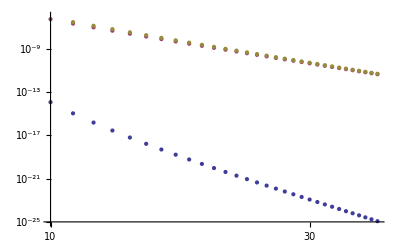

```mathematica
ListLogLogPlot[{dataDirichletNbasis10Error,dataNeumannNbasis10Error,dataNeumannNeumannNbasis10Error},PlotRange->{10^-25,10^-6}]
```

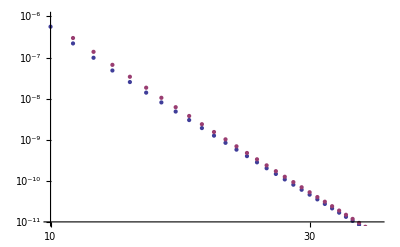

```mathematica
ListLogLogPlot[{dataNeumannNbasis10Error,dataNeumannNeumannNbasis10Error},PlotRange->{10^-11,10^-6}]
```

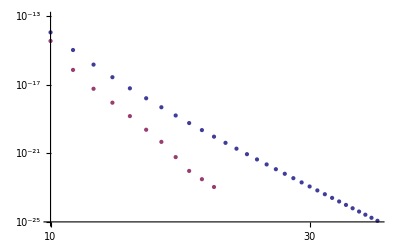

```mathematica
ListLogLogPlot[{dataDirichletNbasis10Error,dataDirichletNbasis10MinimalError},PlotRange->{10^-25,10^-13}]
```

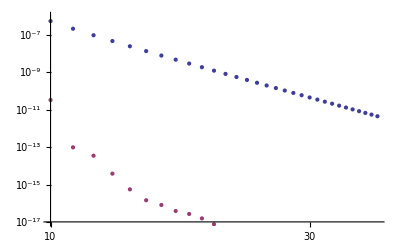

```mathematica
ListLogLogPlot[{dataNeumannNbasis10Error,dataNeumannNbasis10MinimalError},PlotRange->{10^-17,10^-6}]
```

```mathematica
dataDirichletNbasis10MinimalError
```

{{10,7.07100750796030908754311393555029014406768445697815232126886×10^-15}}

```mathematica
Fit[Log[dataDirichletNbasis10Error[[30;;]]],{1,x},x]
```

1.4980050493416245612108729310788538893311360602345687424-15.97084281748847735873152251951981208262274694230422159284 x

```mathematica
Fit[Log[dataNeumannNbasis10Error[[30;;]]],{1,x},x]
```

3.52343687907696800384147215956387589673359777910565661879-8.035681426439804234786133465901831627711787866614612887979 x

```mathematica
DateString[]
```

Mon 3 Feb 2014 21:24:47